```mathematica
f[x_]:=Sin[x]
```

```mathematica
np=4;ni=np-1;dx=2Pi/ni
```

(2 π)/3

```mathematica
xv = Table[i,{i,0,2Pi,dx}]
```

{0,(2 π)/3,(4 π)/3,2 π}

```mathematica
fxv=Table[{xv[[i]],f[xv[[i]]]},{i,1,np}]
```

{{2 π,√(2 π)}}

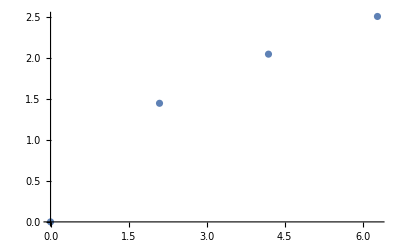

```mathematica
ListPlot[fxv]
```